### Original Code from Steven Wolfram’s Post

#### Simple Game Board

```mathematica
With[{indexMapT=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]]]},
With[{SimplePegGameGraph1={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{2,3,4},{1,4,5}}],
{ReplacePart[Table[1,{5}],({3,3}/.indexMapT)->0]},
UnsameQ@@#&,2,AspectRatio->1/2]},Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][
#2],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]]]
```

-Graphics-

#### Breakdown of Simple Board

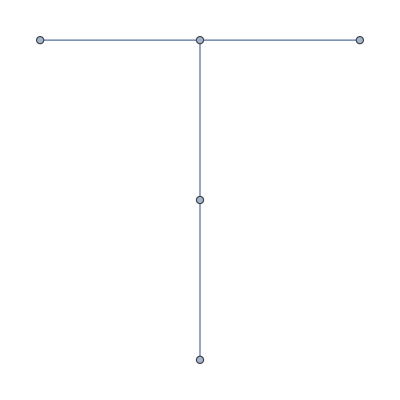

```mathematica
(* 1. creates a nearest neighbor graph and deletes some vertexes for the frame of the board *)
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]
```

```mathematica
VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]]
```

{{1,3},{2,1},{2,2},{2,3},{3,3}}

```mathematica
(* 2. relates each coordinate on the graph and maps it to a number *)
```

```mathematica
indexMapT=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{3,3}],1]],
{{1,1},{1,2},{3,1},{3,2}}]]] (* MapIndexed: #1 is value #2 is index *)
```

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,3}→5}

```mathematica
(* 3. second With function is created to be able to initalize variable SimplePegGameGraph1 without rewriting code *)
```

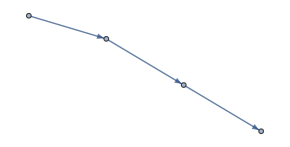

```mathematica
SimplePegGameGraph1={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{2,3,4},{1,4,5}}],
{ReplacePart[Table[1,{5}],({3,3}/.indexMapT)->0]},
UnsameQ@@#&,2,AspectRatio->1/2] (* while there are two pegs next to each other, apply IterateTPSMove over the list of peg states*)
```

```mathematica
Graph[SimplePegGameGraph1 (* node arrangement *),
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}][
#2 (* node statuses *)],#1(* node poisition *),Center,#3(* node size *)]&), VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->{{1,1,1,1,0}->{4,0},{0,1,1,0,1}->{8,0},{0,0,0,1,1}->{12,0},{1,0,0,0,0}->{16,0}}]
```

-Graphics-

```mathematica
MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]
```

{{1,1,1,1,0}→{4,0},{0,1,1,0,1}→{8,0},{0,0,0,1,1}→{12,0},{1,0,0,0,0}→{16,0}}

#### More Complex Game Board

```mathematica
With[{indexMapCross=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{4,4}],1]],{{1,1},{1,2},
{1,4},{2,4},{4,4},{4,3},{3,1},{4,1}}]]]},With[{SimplePegGameGraph2={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}],
{ReplacePart[Table[1,{8}],({1,3}/.indexMapCross)->0]},
UnsameQ@@#&,2]},Graph[SimplePegGameGraph2,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapCross][
#2],#1,Center,#3]&),
VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3]]]
```

-Graphics-

#### Code Breakdown

```mathematica
indexMapCross
```

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,2}→5,{3,3}→6,{3,4}→7,{4,2}→8}

```mathematica
indexMapCross=MapIndexed[#1->#2[[1]]&,VertexList[
VertexDelete[NearestNeighborGraph[Position[
Array[1&,{4,4}],1]],{{1,1},{1,2},
{1,4},{2,4},{4,4},{4,3},{3,1},{4,1}}]]]
```

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,2}→5,{3,3}→6,{3,4}→7,{4,2}→8}

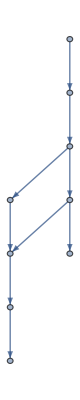

```mathematica
SimplePegGameGraph2={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}, {5,6,8}}],
{ReplacePart[Table[1,{8}],({1,3}/.{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,2}->5,{3,3}->6,{3,4}->7,{4,2}->8})->0]},
UnsameQ@@#&,2]
```

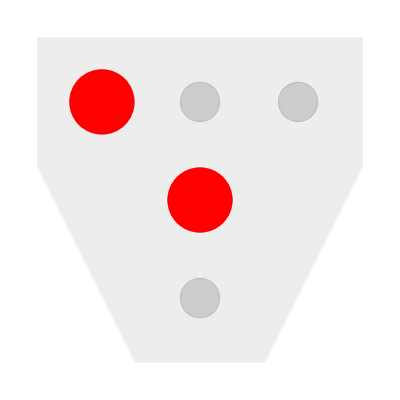

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}][{1,0,1,0,0}]
```

### Personal Implementations

#### Node Layout Generation

```mathematica
(* generates node layout based on all valid moves and starting peg values*)
graphgen[start_,moves_ ]:={{"[◼]", "NestWhileGraph"}}[
{{"[◼]", "IterateTPSMove"}}[moves],
{start},
UnsameQ@@#&,2]
```

```mathematica
graphgen2[start_,moves_ ]:=MyNestWhileGraph[
{{"[◼]", "IterateTPSMove"}}[moves],
{start},
UnsameQ@@#&,2]
```

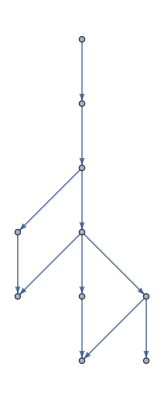

```mathematica
graphgen2[{1,1,0,1,1,1,1,1},{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}]
```

```mathematica
graphgen[{1,1,0,1,1,1,1,1},{{1,4,6},{7,6,5},
{3,5,8},{4,3,2}}]
```

-Graphics-

#### Generating Unique Starting Boards

Currently only works for “square” boards

```mathematica
(* maps each coordinate to a "name" *)
coordnames[coords_] := MapIndexed[#1->#2[[1]]&,coords]
```

```mathematica
visstartingboards[coords_]:= Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][state],{state, Permutations[Append[Table[1, Length[coords]-1],0]]}]
```

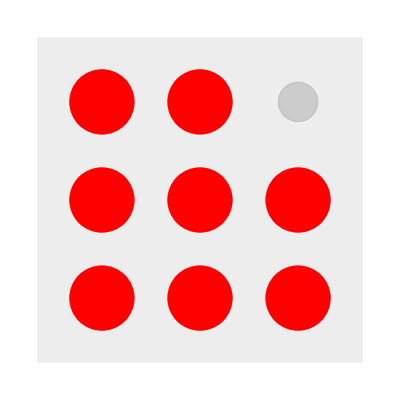
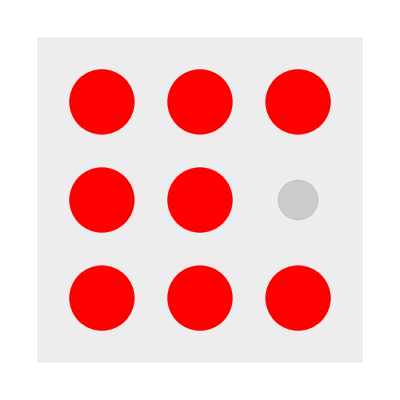
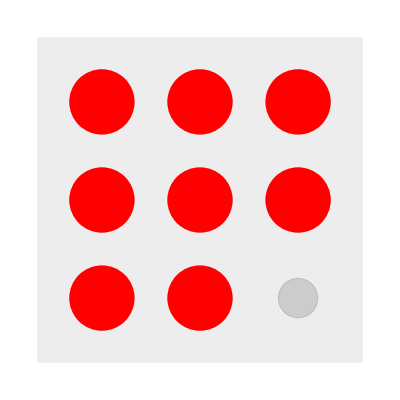
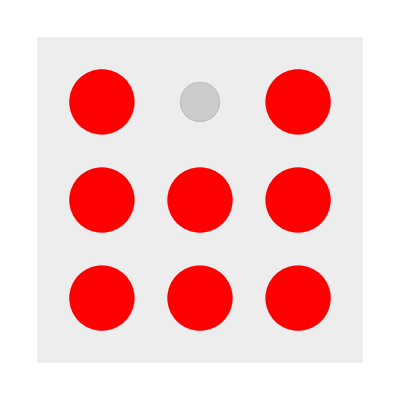
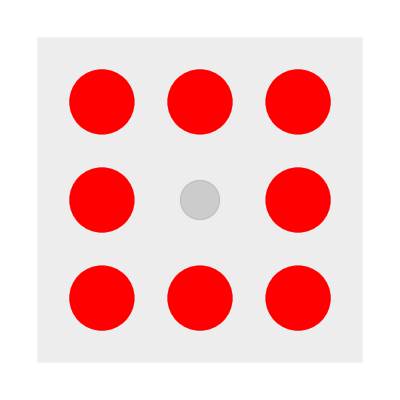
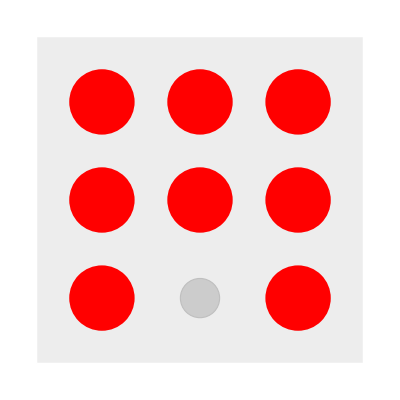
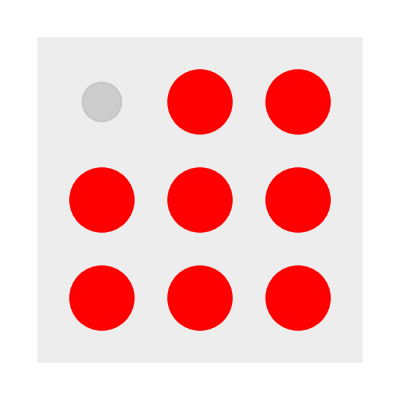
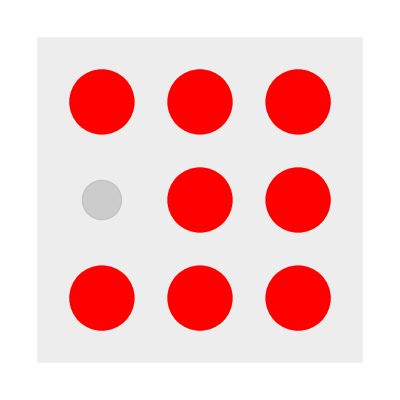

```mathematica
states = visstartingboards[{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}]
```

```mathematica
ImageResize[ImageRotate[-Graphics-],100]===ImageResize[-Graphics-,100]
```

False

```mathematica
ImageDifference[-Graphics-, -Graphics-]
```

-Graphics-

```mathematica
(* If the images are different, the dominate colors of the img difference will not just be black*)
DominantColors[ImageDifference[-Graphics-, -Graphics-]]
```

{RGBColor[0., 2.3370704979557867*^-7, 2.337065217887493*^-7],RGBColor[0.07069081985960773, 0.9292451881270007, 0.9292453343242042]}

```mathematica
DominantColors[ImageDifference[ImageRotate[-Graphics-], -Graphics-]]
```

{RGBColor[0.00010189464294553333, 0.0001024811068795915, 0.00010248110427860364]}

```mathematica
(* compares two images and checks if they are the same *)
compareImg[img1_, img2_]:=If[Length[DominantColors[ImageDifference[ImageRotate[img1, 90 Degree], img2]]] ==1 || Length[DominantColors[ImageDifference[ImageRotate[img1, 180 Degree], img2]]]==1 || Length[DominantColors[ImageDifference[ImageRotate[img1, 270 Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageReflect[img1], img2]]]==1||
Length[DominantColors[ImageDifference[ImageReflect[img1, Left], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],90Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],180Degree], img2]]]==1 ||
Length[DominantColors[ImageDifference[ImageRotate[ImageReflect[img1],270Degree], img2]]]==1,
True, False]
```

```mathematica
(* checks if an image is already represented in a list *)
uniqueImg[img_, uniques_] := Which[Length[uniques] ==1, Not[compareImg[img, uniques[[1]]]],
Position[compareImg@@@Partition[Riffle[uniques,img, {2, -1, 2}],2],True] == {}, True, True, False]
```

```mathematica
(* create a list of unique elements *)
getUnique[statelist_] := 
Block[{states = statelist, uniques = {statelist[[1]]}},
If[uniqueImg[#, uniques], AppendTo[uniques, #]]&/@states[[2;;]]; uniques]
```

```mathematica
getUnique[visstartingboards[{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
compareImg[-Graphics-,-Graphics-]
```

False

#### Creating Multiway Graphs with Visuals

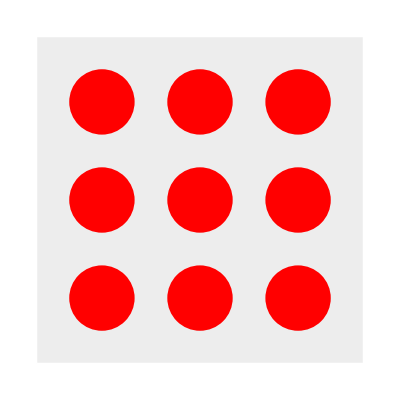

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[#1][#2]&[coordnames[{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}],{1,1,1,1,1,1,1,1,1,1}]
```

```mathematica
graph1=Graph[GraphData["PetersenGraph"],VertexLabels->"Name"](*example graph*)
VertexContract[graph1,DeleteDuplicates[Table[Select[VertexList[graph1],Mod[#,7]==Mod[i,7]&(*test function*)],{i,VertexList[graph1]}]]]
```

```mathematica
(* create multiway graphs given a set of coordinates for a board, the starting positions of pegs, and all of the possible moves *)

(* multiwaygraph[list of coords (no names), starting state, possible moves] *)
multiwaygraph[coords_, start_, moves_] := Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[coords]][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3]
```

```mathematica
(* create multiway graphs without duplicate boards given a set of coordinates for a board, the starting positions of pegs, all of the possible moves, and a square board *)

(* multiwaygraph2[list of coords (no names), starting state, possible moves] *)
multiwaygraph2[coordlist_, starting_, allmoves_] := Module[{coords = coordnames[coordlist], start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], Association[Reverse/@Normal[coords]]];
VertexContract[graph, Gather[VertexList[graph],compareImg[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords]][#1], {{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords]][#2]] ==True&]]
]
```

```mathematica
boardcoords = ReplacePart[VertexList[multiwaygraph[coords,start,moves]][[1]], Association[Reverse/@Normal[coords]]]
coordnames[boardcoords]
```

{{1,3},{2,1},{2,2},{2,3},{3,2},{3,3},{3,4},{4,2}}

{{1,3}→1,{2,1}→2,{2,2}→3,{2,3}→4,{3,2}→5,{3,3}→6,{3,4}→7,{4,2}→8}

```mathematica
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
```

```mathematica
multiwaygraph2[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}},{0,1,1,1,1,1,1,1,1},{{1,2,3},{1,5,9},{1,4,7},{2,5,8},{3,5,7},{3,6,9},{4,5,6},{7,8,9}}]
```

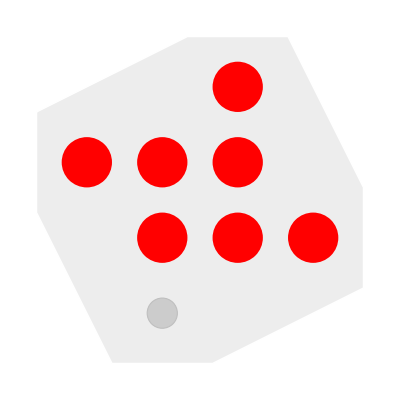
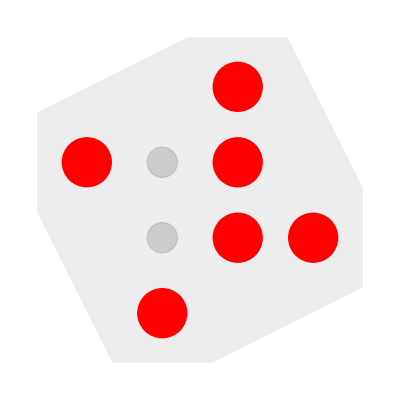
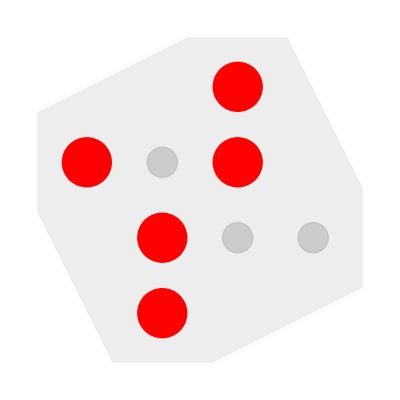
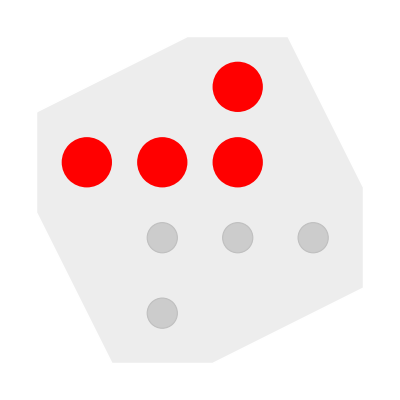
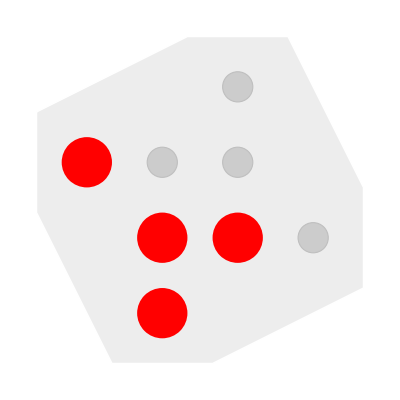
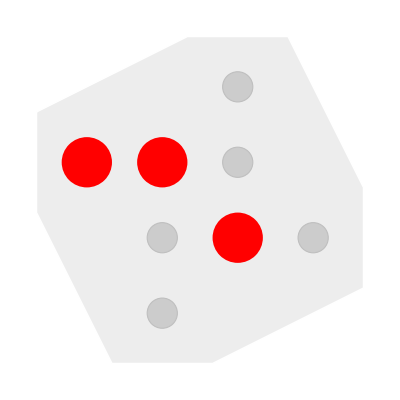
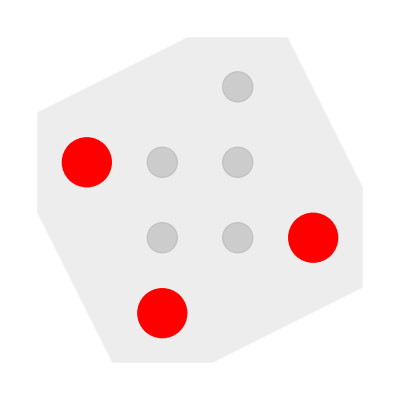
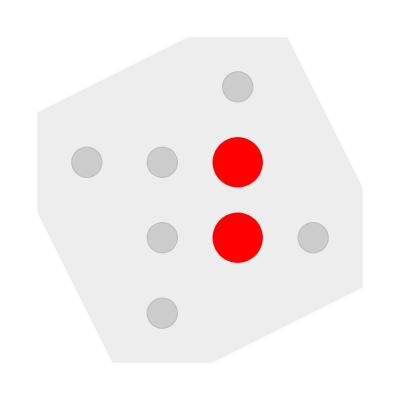

```mathematica
uniques = getUnique[Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[Table[ReplacePart[VertexList[graph][[i]], Association[Reverse/@Normal[coords]]],{i, Range[Length[VertexList[graph]]]}][[1]]]][state],{state, VertexList[graph]}]]
```

```mathematica
coords = {{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,2}->5,{3,3}->6,{3,4}->7,{4,2}->8};
start = {1,0,1,1,1,1,1,1};
moves = {{1,4,6},{7,6,5},
{3,5,8},{4,3,2}};
```

```mathematica
Keys[coords]
```

{{1,3},{2,1},{2,2},{2,3},{3,2},{3,3},{3,4},{4,2}}

Multiway Graph Testing :)

```mathematica
graph2 = multiwaygraph[{{1,1}->1,{2,1}->2,{3,1}->3,{1,2}->4,{2,2}->5,{3,2}->6,{1,3}->7,{2,3}->8,{3,3}->9},{0,1,1,1,1,1,1,1,1},{{1,2,3},{1,5,9},{1,4,7},{2,5,8},{3,5,7},{3,6,9},{4,5,6},{7,8,9}}];
```

```mathematica
coords2 = {{1,1}->1,{2,1}->2,{3,1}->3,{1,2}->4,{2,2}->5,{3,2}->6,{1,3}->7,{2,3}->8,{3,3}->9};
start2  = {0,1,1,1,1,1,1,1,1};
moves2 = {{1,2,3},{1,5,9},{1,4,7},{2,5,8},{3,5,7},{3,6,9},{4,5,6},{7,8,9}};
```

```mathematica
boardcoords2 = ReplacePart[VertexList[multiwaygraph[coords2,start2,moves2]][[1]], Association[Reverse/@Normal[coords2]]];
allboards2 =VertexList[graph2];
```

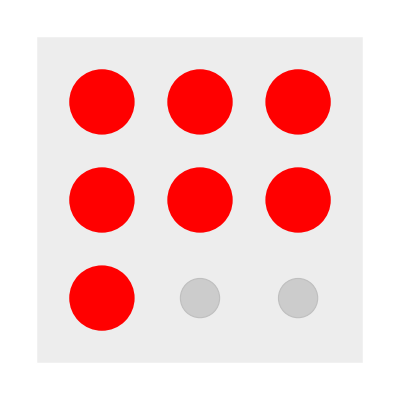
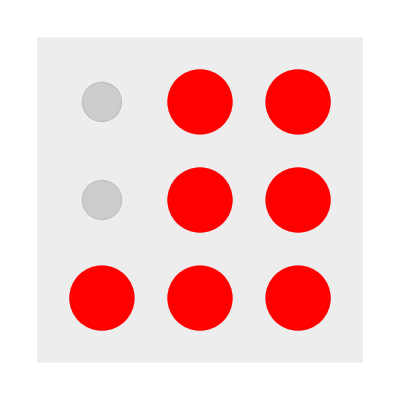
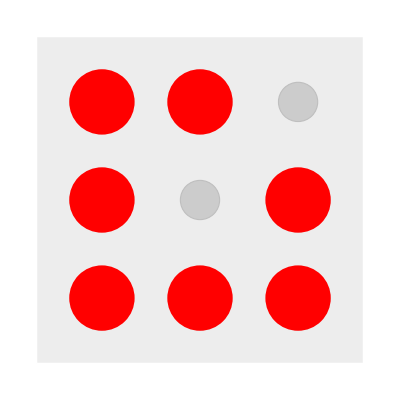
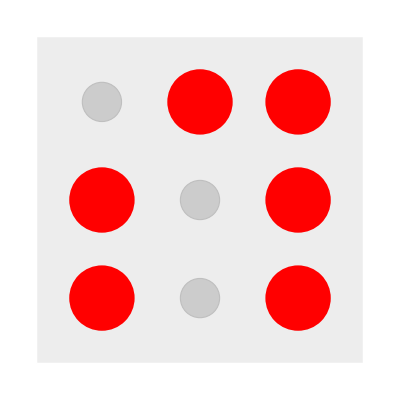
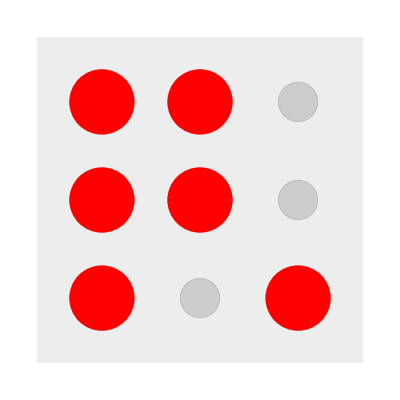
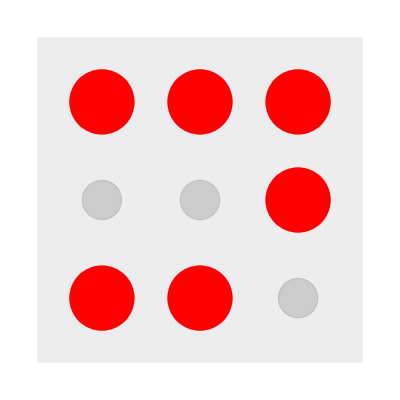
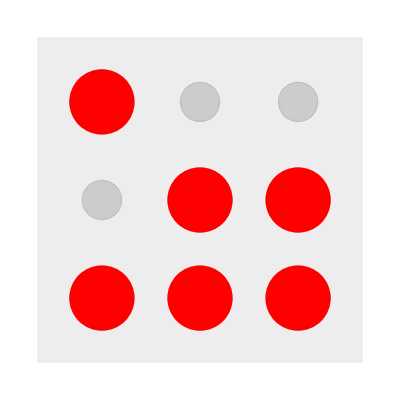
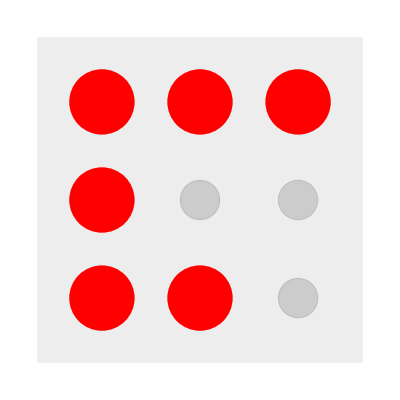
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
getUnique[Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords2]][state],{state, allboards2}]]
```

```mathematica
getUnique[Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[boardcoords2]][state],{state, allboards2}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
multiwaygraph2[coords,start,moves]
```

-Graphics-

```mathematica
VertexList[multiwaygraph[coords,start,moves]]
```

{{1,0,1,1,1,1,1,1},{1,1,0,0,1,1,1,1},{1,1,1,0,0,1,1,0},{1,0,0,1,0,1,1,0},{1,1,1,0,1,0,0,0},{1,0,0,1,1,0,0,0},{1,1,0,0,0,0,0,1},{0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,0}}

```mathematica
multiwaygraph[coords,start,moves]
```

-Graphics-

```mathematica
multiwaygraph[coords,{1,1,1,0,0,0,0,0},moves]
```

-Graphics-

```mathematica
multiwaygraph[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6},{1,1,1,1,1,0},{{1,3,6},{1,2,4},{4,5,6}}]
```

-Graphics-

```mathematica
multiwaygraph[{{1,1}->1,{2,1}->2,{3,1}->3,{1,2}->4,{2,2}->5,{3,2}->6,{1,3}->7,{2,3}->8,{3,3}->9},{0,1,1,1,1,1,1,1,1},{{1,2,3},{1,5,9},{1,4,7},{2,5,8},{3,5,7},{3,6,9},{4,5,6},{7,8,9}}]
```

-Graphics-

```mathematica
multiwaygraph2[{{1,1}->1,{2,1}->2,{3,1}->3,{1,2}->4,{2,2}->5,{3,2}->6,{1,3}->7,{2,3}->8,{3,3}->9},{0,1,1,1,1,1,1,1,1},{{1,2,3},{1,5,9},{1,4,7},{2,5,8},{3,5,7},{3,6,9},{4,5,6},{7,8,9}}]
```

-Graphics-

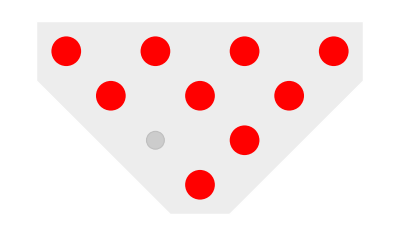
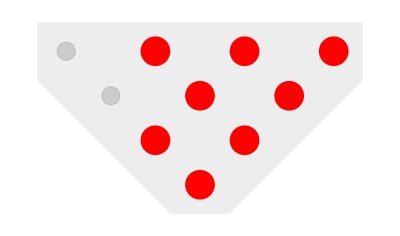
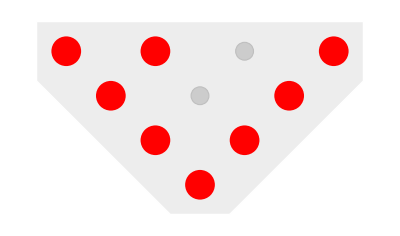
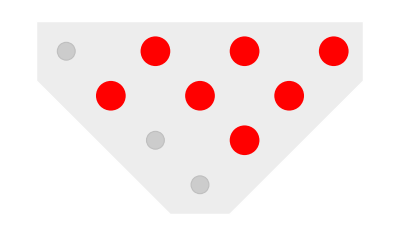
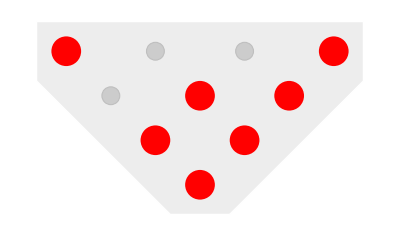
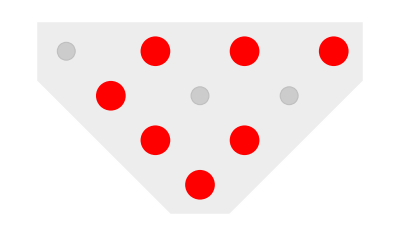
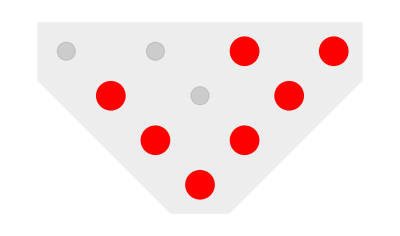
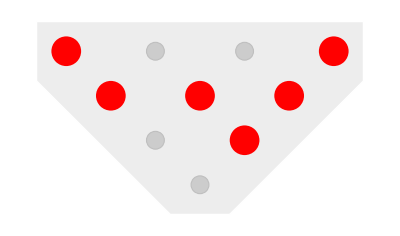

```mathematica
multiwaygraph[{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}->9, {3,3}->10},{1,0,1,1,1,1,1,1,1,1},{{1,3,6},{1,2,4},{2,5,9},{2,4,7},{3,6,10},{4,5,6},{7,8,9}}]
```

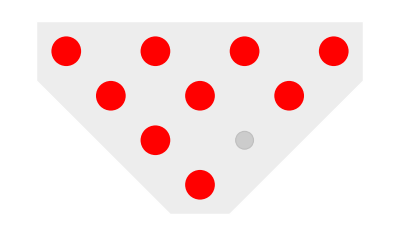
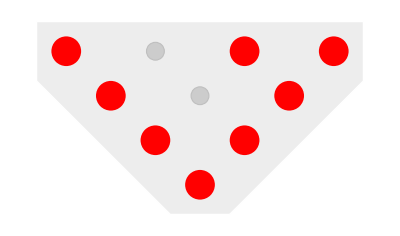

```mathematica
multiwaygraph[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10},{1,1,0,1,1,1,1,1,1,1},{{1,3,6},{1,2,4},{2,5,9},{2,4,7},{3,5,8},{3,6,10},{4,5,6},{7,8,9},{8,9,10}}]
```

#### Calculating Possible Moves

```mathematica
EuclideanDistance[{3,3},{-3,3}]
```

6

```mathematica
distance[{-3,3}, {3,3}]
```

6

```mathematica
Sqrt[(n[[1]] - m[[1]])^2 + (n[[2]] - m[[2]])^2]
```

6

```mathematica
m = {3,3};
n = {-3,3};
(n[[1]] - m[[1]])^2;
(n[[2]] - m[[2]])^2;
(n[[1]] - m[[1]])^2 + (n[[2]] - m[[2]])^2;
Sqrt[(n[[1]] - m[[1]])^2 + (n[[2]] - m[[2]])^2]
```

6

```mathematica
{3,3}[[2]]
```

3

```mathematica
checkshape[makeimg[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10}]]
```

square

```mathematica
(* calculates the points next to a specified peg given the coordinates of a square*)
getNear[coords_, peg_, shape_/; shape=="square"] := Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] < 2 && (coord[[1]] == peg[[1]] || coord[[2]] == peg[[2]]), coord],{coord, coords}], ListQ]]
```

```mathematica
(* getNear but for a triangle *)
getNear[coords_, peg_, shape_/; shape=="triangle"] := Delete[#, Position[#, peg]]&[Select[Table[Which[EuclideanDistance[peg, coord] < 2 || And[peg[[2]]==coord[[2]],EuclideanDistance[peg, coord] == 2], coord],{coord, coords}], ListQ]]
```

```mathematica
getNear[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10}, {3,3},checkshape[makeimg[{{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}]]]
```

{}

```mathematica
(* given a peg and a list of coordinates, finds all the possible moves that peg could be in *)
pegMoves[initalpeg_, coordlist_] :=Module[{peg = initalpeg, coords = coordlist, moves = {}, peg2s, peg3s},
peg2s = getNear[coords, peg, checkshape[makeimg[coords]]];
peg3s = Table[{peg2[[1]]+(peg2[[1]] - peg[[1]]), peg2[[2]]+(peg2[[2]]-peg[[2]])}, {peg2, peg2s}];
Select[Table[If[Position[coords,peg3s[[i]]] != {},{peg, peg2s[[i]], peg3s[[i]]}], {i, Range[Length[peg2s]]}], ListQ]
]
```

```mathematica
pegMoves[{3,3}, {{0,0},{-1,1},{1,1},{-2,2},{0,2},{2,2},{-3,3},{-1,3},{1,3}, {3,3}}]
```

{{{3,3},{2,2},{1,1}},{{3,3},{1,3},{-1,3}}}

```mathematica
(* maps through all pegs in a peg list and find all possible moves *)
allMoves[coordlist_] := Module[{coords = coordlist, moves = {}},
ResourceFunction["JoinTo"][moves, pegMoves[#, coords] /. coordnames[coords] &/@ coords];
Flatten[DeleteDuplicates[moves],1]
]
```

```mathematica
(* 3 x 3 square *)
allMoves[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}}]
```

{{1,2,3},{1,4,7},{2,5,8},{3,2,1},{3,6,9},{4,5,6},{6,5,4},{7,4,1},{7,8,9},{8,5,2},{9,6,3},{9,8,7}}

```mathematica
(* 4 base triangle *)
allMoves[{{0,0}->1,{1,1}->2,{-1,1}->3,{2,2}->4,{0,2}->5,{-2,2}->6,{3,3}->7,{1,3}->8,{-1,3}->9, {-3,3}->10}]
```

{{1,2,4},{1,3,6},{2,4,7},{2,5,9},{3,5,8},{3,6,10},{4,2,1},{4,5,6},{6,3,1},{6,5,4},{7,4,2},{7,8,9},{8,5,3},{8,9,10},{9,5,2},{9,8,7},{10,6,3},{10,9,8}}

```mathematica
pegMoves[{3,3}, {{0,0}->1,{1,1}->2,{-1,1}->3,{2,2}->4,{0,2}->5,{-2,2}->6,{3,3}->7,{1,3}->8,{-1,3}->9, {-3,3}->10}]
```

{{{3,3},{2,2},{1,1}}}

```mathematica
makeimg[points_ ] := 
Graphics[{PointSize[Large],Point[Table[p,{p,points}]]}]
```

```mathematica
makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}}]
```

-Graphics-

```mathematica
lines = ImageLines[-Graphics-];
HighlightImage[-Graphics-, lines]
```

-Graphics-

```mathematica
(* Trying to train a classify function to identify shapes*)
```

triangle data:

```mathematica
triangle = {makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2}}],
makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}}], makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7},{8,8},{6,8},{4,8},{2,8},{0,8},{-2,8},{-4,8},{-6,8},{-8,8},{9,9},{7,9},{5,9},{3,9},{1,9},{-1,9},{-3,9},{-5,9},{-7,9},{-9,9}}],makeimg[{{0,0},{1,1},{-1,1},{2,2},{0,2},{-2,2},{3,3},{1,3},{-1,3}, {-3,3}, {4,4}, {2,4}, {0,4}, {-2,4}, {-4,4}, {5,5}, {3, 5}, {1,5}, {-1, 5}, {-3,5}, {-5,5}, {6,6}, {4,6}, {2,6}, {0,6}, {-2,6}, {-4, 6}, {-6,6},{7,7},{5,7},{3,7},{1,7},{-1,7},{-3,7},{-5,7},{-7,7},{8,8},{6,8},{4,8},{2,8},{0,8},{-2,8},{-4,8},{-6,8},{-8,8},{9,9},{7,9},{5,9},{3,9},{1,9},{-1,9},{-3,9},{-5,9},{-7,9},{-9,9},{10,10},{8,10},{6,10},{4,10},{2,10},{0,10},{-2,10},{-4,10},{-6,10},{-8,10},{-10,10}}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

square data:

```mathematica
square = {makeimg[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2}, {1,3}, {2,3},{3,3}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2}, {1,3}, {2,3},{3,3},{4,3},{1,4},{2,4},{3,4},{4,4}}],makeimg[{{2,1},{3,1},{1,2},{2,2},{3,2},{4,2}, {1,3}, {2,3},{3,3},{4,3},{2,4},{3,4}}] ,makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4},{1,5},{2,5},{3,5},{4,5},{5,5}}], makeimg[{{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{1,4},{2,4},{3,4},{4,4},{5,4},{2,5},{3,5},{4,5}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6}}],makeimg[{{3,1},{4,1},{3,2},{4,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{3,5},{4,5},{3,6},{4,6}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7}}],makeimg[{{3,1},{4,1},{5,1},{3,2},{4,2},{5,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{3,6},{4,6},{5,6},{3,7},{4,7},{5,7}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7}}],makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8}}],makeimg[{{3,1},{4,1},{5,1},{6,1},{3,2},{4,2},{5,2},{6,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{3,7},{4,7},{5,7},{6,7},{3,8},{4,8},{5,8},{6,8}}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
checkshape = Classify[<|"square" -> square, "triangle" ->triangle|>]
```

ClassifierFunction[…]

```mathematica
checkshape[makeimg[{{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{1,2},{2,2},{3,2},{4,2},{5,2},{6,2},{7,2},{8,2},{9,2},{1,3},{2,3},{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{9,3},{1,4},{2,4},{3,4},{4,4},{5,4},{6,4},{7,4},{8,4},{9,4},{1,5},{2,5},{3,5},{4,5},{5,5},{6,5},{7,5},{8,5},{9,5},{1,6},{2,6},{3,6},{4,6},{5,6},{6,6},{7,6},{8,6},{9,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{7,7},{8,7},{9,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{8,8},{9,8}}]]
```

square

#### Trying to delete “duplicate”/rotated boards

Nest While Graph

```mathematica
EdgesConstruct[edges_,in_,outs_List]:=edges[in,#]&/@outs
```

```mathematica
EdgesConstruct[edges_,in_,out_]:=edges[in,out]
```

```mathematica
ListNewEdges[state_,fun_,True]:=Union[
Flatten[MapThread[
EdgesConstruct[DirectedEdge,#1,#2]&,
{state[[2]],fun/@state[[2]]}]]]
```

```mathematica
ListNewEdges[state_,fun_,False]:=Union[
Flatten[MapThread[
EdgesConstruct[UndirectedEdge,#1,#2]&,
{state[[2]],fun/@state[[2]]}]]]
```

```mathematica
IterateState[state_,newEdges_,True]:=
{EdgeAdd[state[[1]],newEdges],
Complement[newEdges[[All,2]],state[[3]]  ],
Union[state[[3]],newEdges[[All,2]]],
{}
}
```

```mathematica
IterateState[state_,newEdges_,False]:=
With[{sortedEdges=Map[Sort,newEdges]},
{EdgeAdd[state[[1]],
Complement[sortedEdges,state[[4]] ]],
Complement[newEdges[[All,2]],state[[3]]  ],
Union[state[[3]],newEdges[[All,2]]],
Union[state[[4]],sortedEdges]
}]
```

```mathematica
ConditionalTest[states_,test_,1]:=test[states[[-1]]]
```

```mathematica
ConditionalTest[states_,test_,All
]:=test[Map[states[[-#]]&,
Reverse[Range[Length[states]]]]]
```

```mathematica
ConditionalTest[states_,test_,many_Integer
]:=If[Or[Length[states]>=many,SameQ[many,All]],
test[states[[-#]]&/@Reverse[Range[many]]],True]
```

```mathematica
MyNestWhileGraph[fun_,init_Graph,test_,
many:(_Integer|All):1,
max:(_Integer|Infinity):Infinity,
opts:OptionsPattern[Graph]]:=With[{
dirTF=If[SameQ[
OptionValue[DirectedEdges],False],False,True]},
Graph[NestWhile[
IterateState[#,ListNewEdges[#,fun,dirTF],dirTF]&,
{init,VertexList[init],VertexList[init],EdgeList[init]},
ConditionalTest[{##}[[All,1]],test,many]&,
many,max][[1]],opts]]
```

```mathematica
MyNestWhileGraph[fun_,init_,test_,
many:(_Integer|All):1,
max:(_Integer|Infinity):Infinity,
opts:OptionsPattern[Graph]]:=With[{
dirTF=If[SameQ[
OptionValue[DirectedEdges],False],False,True]
},
Graph[NestWhile[
IterateState[#,ListNewEdges[#,fun,dirTF],dirTF]&,
{Graph[{init},{}],{init},{init},{}},
ConditionalTest[{##}[[All,1]],test,many]&,
many,max][[1]],opts]]
```

```mathematica
MyNestWhileGraph[fun_,init_List,test_,
many:(_Integer|All):1,
max:(_Integer|Infinity):Infinity,
opts:OptionsPattern[Graph]]:=With[{
dirTF=If[SameQ[
OptionValue[DirectedEdges],False],False,True]},
Graph[NestWhile[
IterateState[#,ListNewEdges[#,fun,dirTF],dirTF]&,
{Graph[init,{}],init,init,{}},
ConditionalTest[{##}[[All,1]],test,many]&,
many,max][[1]],opts]]
```

#### Secondary way of deleting “duped” boards

```mathematica
fourcoords = {{1,1},{2,1},{3,1},{4,1},{1,2},{2,2},{3,2},{4,2}, {1,3}, {2,3},{3,3},{4,3},{1,4},{2,4},{3,4},{4,4}};
fourmoves = allMoves[fourcoords];
```

```mathematica
visstartingboards[fourcoords]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
compareSqrList[list1_, list2_] := Module[{length = Sqrt[Length[list1]]},
lists1 = Partition[list1, length];
lists2 = Partition[list2, length];
If[Transpose @(Reverse/@lists1)==lists2 ||
Reverse/@(Transpose @lists1)==lists2 ||
Transpose @(Reverse/@(Transpose @(Reverse/@lists1)))==lists2 ||
Transpose @(Reverse/@(Transpose @lists1)) == lists2||
Reverse/@(Transpose @(Reverse/@lists1)) == lists2||
Transpose @lists1 ==lists2 ||
Reverse/@lists1 ==lists2
,True,False]
]
```

```mathematica
compareSqrList[{0,0,0,1,0,0,1,1,1}, {0,0,0,0,0,1,1,1,1}]
```

True

```mathematica
compareSqrList[{0,1,1,1,1,1,1,1,1}, {1,1,0,1,1,1,1,1,1}]
```

If[(Transpose=={{1,1,0},{1,1,1},{1,1,1}})[Transpose[True]],True,False]

```mathematica
compareSqrList[{0,1,1,1,1,1,1,1,1}, {1,1,1,0,1,1,1,1,1}]
```

False

```mathematica
compareSqrList[{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}, {1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1}]
```

True

```mathematica
(* create multiway graphs without duplicate boards given a set of coordinates for a board, the starting positions of pegs, all of the possible moves, and a square board *)

(* multiwaygraph2[list of coords (no names), starting state, possible moves] *)
multiwaygraph3[coordlist_, starting_, allmoves_] := Module[{coords = coordnames[coordlist], start = starting, moves = allmoves},
graph = Graph[graphgen[start, moves],VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[coords][
#2],#1,Center,#3]&),VertexSize->1.2,PerformanceGoal->"Quality",EdgeStyle->Gray,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->3];
boardcoords = ReplacePart[VertexList[graph][[1]], Association[Reverse/@Normal[coords]]];
VertexContract[graph, Gather[VertexList[graph],compareSqrList[#1,#2] ==True&]]
]
```

```mathematica
multiwaygraph[fourcoords,{ 0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}, fourmoves]
```

-Graphics-

```mathematica
getNear[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}}, {3,3},checkshape[makeimg[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}}]]]
```

{{3,2},{2,3}}

```mathematica
allMoves[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}}]
```

{{1,2,3},{1,4,7},{2,5,8},{3,2,1},{3,6,9},{4,5,6},{6,5,4},{7,4,1},{7,8,9},{8,5,2},{9,6,3},{9,8,7}}

```mathematica
multiwaygraph3[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}},{0,1,1,1,1,1,1,1,1},allMoves[{{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}}]]
```

-Graphics-

```mathematica
multiwaygraph3[fourcoords,{ 0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}, fourmoves]
```

-Graphics-

#### Analyzing 3x3 boards

```mathematica
threecoords = {{1,1},{2,1},{3,1},{1,2},{2,2},{3,2},{1,3},{2,3},{3,3}};
threemoves = allMoves[threecoords];
```

```mathematica
multiwaygraph3[threecoords,{0,1,1,1,1,1,1,1,1}, threemoves ]
```

-Graphics-

```mathematica
VertexList[%]
```

{{0,1,1,1,1,1,1,1,1},{1,0,0,1,1,1,1,1,1},{1,0,1,1,1,0,1,1,0},{1,1,0,1,0,1,1,0,1},{1,0,1,0,0,1,1,1,0},{1,0,1,1,1,0,0,0,1},{1,1,1,1,0,0,1,0,0},{0,0,1,1,0,1,1,0,1},{1,0,1,0,0,1,0,0,1},{0,0,1,0,1,0,1,0,1}}

```mathematica
Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0},{1,0,0,1,0,0,0,0,0},{1,0,0,0,1,0,0,0,0},{1,0,0,0,0,1,0,0,0},{1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,0,1,0},{1,0,0,0,0,0,0,0,1},{0,1,1,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,1,0,0,1,0,0,0,0},{0,1,0,0,0,1,0,0,0},{0,1,0,0,0,0,1,0,0},{0,1,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0,1},{0,0,1,1,0,0,0,0,0},{0,0,1,0,1,0,0,0,0},{0,0,1,0,0,1,0,0,0},{0,0,1,0,0,0,1,0,0},{0,0,1,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,1},{0,0,0,1,1,0,0,0,0},{0,0,0,1,0,1,0,0,0},{0,0,0,1,0,0,1,0,0},{0,0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,0,1},{0,0,0,0,1,1,0,0,0},{0,0,0,0,1,0,1,0,0},{0,0,0,0,1,0,0,1,0},{0,0,0,0,1,0,0,0,1},{0,0,0,0,0,1,1,0,0},{0,0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,1,1},{1,1,1,0,0,0,0,0,0},{1,1,0,1,0,0,0,0,0},{1,1,0,0,1,0,0,0,0},{1,1,0,0,0,1,0,0,0},{1,1,0,0,0,0,1,0,0},{1,1,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,1},{1,0,1,1,0,0,0,0,0},{1,0,1,0,1,0,0,0,0},{1,0,1,0,0,1,0,0,0},{1,0,1,0,0,0,1,0,0},{1,0,1,0,0,0,0,1,0},{1,0,1,0,0,0,0,0,1},{1,0,0,1,1,0,0,0,0},{1,0,0,1,0,1,0,0,0},{1,0,0,1,0,0,1,0,0},{1,0,0,1,0,0,0,1,0},{1,0,0,1,0,0,0,0,1},{1,0,0,0,1,1,0,0,0},{1,0,0,0,1,0,1,0,0},{1,0,0,0,1,0,0,1,0},{1,0,0,0,1,0,0,0,1},{1,0,0,0,0,1,1,0,0},{1,0,0,0,0,1,0,1,0},{1,0,0,0,0,1,0,0,1},{1,0,0,0,0,0,1,1,0},{1,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,1,1},{0,1,1,1,0,0,0,0,0},{0,1,1,0,1,0,0,0,0},{0,1,1,0,0,1,0,0,0},{0,1,1,0,0,0,1,0,0},{0,1,1,0,0,0,0,1,0},{0,1,1,0,0,0,0,0,1},{0,1,0,1,1,0,0,0,0},{0,1,0,1,0,1,0,0,0},{0,1,0,1,0,0,1,0,0},{0,1,0,1,0,0,0,1,0},{0,1,0,1,0,0,0,0,1},{0,1,0,0,1,1,0,0,0},{0,1,0,0,1,0,1,0,0},{0,1,0,0,1,0,0,1,0},{0,1,0,0,1,0,0,0,1},{0,1,0,0,0,1,1,0,0},{0,1,0,0,0,1,0,1,0},{0,1,0,0,0,1,0,0,1},{0,1,0,0,0,0,1,1,0},{0,1,0,0,0,0,1,0,1},{0,1,0,0,0,0,0,1,1},{0,0,1,1,1,0,0,0,0},{0,0,1,1,0,1,0,0,0},{0,0,1,1,0,0,1,0,0},{0,0,1,1,0,0,0,1,0},{0,0,1,1,0,0,0,0,1},{0,0,1,0,1,1,0,0,0},{0,0,1,0,1,0,1,0,0},{0,0,1,0,1,0,0,1,0},{0,0,1,0,1,0,0,0,1},{0,0,1,0,0,1,1,0,0},{0,0,1,0,0,1,0,1,0},{0,0,1,0,0,1,0,0,1},{0,0,1,0,0,0,1,1,0},{0,0,1,0,0,0,1,0,1},{0,0,1,0,0,0,0,1,1},{0,0,0,1,1,1,0,0,0},{0,0,0,1,1,0,1,0,0},{0,0,0,1,1,0,0,1,0},{0,0,0,1,1,0,0,0,1},{0,0,0,1,0,1,1,0,0},{0,0,0,1,0,1,0,1,0},{0,0,0,1,0,1,0,0,1},{0,0,0,1,0,0,1,1,0},{0,0,0,1,0,0,1,0,1},{0,0,0,1,0,0,0,1,1},{0,0,0,0,1,1,1,0,0},{0,0,0,0,1,1,0,1,0},{0,0,0,0,1,1,0,0,1},{0,0,0,0,1,0,1,1,0},{0,0,0,0,1,0,1,0,1},{0,0,0,0,1,0,0,1,1},{0,0,0,0,0,1,1,1,0},{0,0,0,0,0,1,1,0,1},{0,0,0,0,0,1,0,1,1},{0,0,0,0,0,0,1,1,1},{1,1,1,1,0,0,0,0,0},{1,1,1,0,1,0,0,0,0},{1,1,1,0,0,1,0,0,0},{1,1,1,0,0,0,1,0,0},{1,1,1,0,0,0,0,1,0},{1,1,1,0,0,0,0,0,1},{1,1,0,1,1,0,0,0,0},{1,1,0,1,0,1,0,0,0},{1,1,0,1,0,0,1,0,0},{1,1,0,1,0,0,0,1,0},{1,1,0,1,0,0,0,0,1},{1,1,0,0,1,1,0,0,0},{1,1,0,0,1,0,1,0,0},{1,1,0,0,1,0,0,1,0},{1,1,0,0,1,0,0,0,1},{1,1,0,0,0,1,1,0,0},{1,1,0,0,0,1,0,1,0},{1,1,0,0,0,1,0,0,1},{1,1,0,0,0,0,1,1,0},{1,1,0,0,0,0,1,0,1},{1,1,0,0,0,0,0,1,1},{1,0,1,1,1,0,0,0,0},{1,0,1,1,0,1,0,0,0},{1,0,1,1,0,0,1,0,0},{1,0,1,1,0,0,0,1,0},{1,0,1,1,0,0,0,0,1},{1,0,1,0,1,1,0,0,0},{1,0,1,0,1,0,1,0,0},{1,0,1,0,1,0,0,1,0},{1,0,1,0,1,0,0,0,1},{1,0,1,0,0,1,1,0,0},{1,0,1,0,0,1,0,1,0},{1,0,1,0,0,1,0,0,1},{1,0,1,0,0,0,1,1,0},{1,0,1,0,0,0,1,0,1},{1,0,1,0,0,0,0,1,1},{1,0,0,1,1,1,0,0,0},{1,0,0,1,1,0,1,0,0},{1,0,0,1,1,0,0,1,0},{1,0,0,1,1,0,0,0,1},{1,0,0,1,0,1,1,0,0},{1,0,0,1,0,1,0,1,0},{1,0,0,1,0,1,0,0,1},{1,0,0,1,0,0,1,1,0},{1,0,0,1,0,0,1,0,1},{1,0,0,1,0,0,0,1,1},{1,0,0,0,1,1,1,0,0},{1,0,0,0,1,1,0,1,0},{1,0,0,0,1,1,0,0,1},{1,0,0,0,1,0,1,1,0},{1,0,0,0,1,0,1,0,1},{1,0,0,0,1,0,0,1,1},{1,0,0,0,0,1,1,1,0},{1,0,0,0,0,1,1,0,1},{1,0,0,0,0,1,0,1,1},{1,0,0,0,0,0,1,1,1},{0,1,1,1,1,0,0,0,0},{0,1,1,1,0,1,0,0,0},{0,1,1,1,0,0,1,0,0},{0,1,1,1,0,0,0,1,0},{0,1,1,1,0,0,0,0,1},{0,1,1,0,1,1,0,0,0},{0,1,1,0,1,0,1,0,0},{0,1,1,0,1,0,0,1,0},{0,1,1,0,1,0,0,0,1},{0,1,1,0,0,1,1,0,0},{0,1,1,0,0,1,0,1,0},{0,1,1,0,0,1,0,0,1},{0,1,1,0,0,0,1,1,0},{0,1,1,0,0,0,1,0,1},{0,1,1,0,0,0,0,1,1},{0,1,0,1,1,1,0,0,0},{0,1,0,1,1,0,1,0,0},{0,1,0,1,1,0,0,1,0},{0,1,0,1,1,0,0,0,1},{0,1,0,1,0,1,1,0,0},{0,1,0,1,0,1,0,1,0},{0,1,0,1,0,1,0,0,1},{0,1,0,1,0,0,1,1,0},{0,1,0,1,0,0,1,0,1},{0,1,0,1,0,0,0,1,1},{0,1,0,0,1,1,1,0,0},{0,1,0,0,1,1,0,1,0},{0,1,0,0,1,1,0,0,1},{0,1,0,0,1,0,1,1,0},{0,1,0,0,1,0,1,0,1},{0,1,0,0,1,0,0,1,1},{0,1,0,0,0,1,1,1,0},{0,1,0,0,0,1,1,0,1},{0,1,0,0,0,1,0,1,1},{0,1,0,0,0,0,1,1,1},{0,0,1,1,1,1,0,0,0},{0,0,1,1,1,0,1,0,0},{0,0,1,1,1,0,0,1,0},{0,0,1,1,1,0,0,0,1},{0,0,1,1,0,1,1,0,0},{0,0,1,1,0,1,0,1,0},{0,0,1,1,0,1,0,0,1},{0,0,1,1,0,0,1,1,0},{0,0,1,1,0,0,1,0,1},{0,0,1,1,0,0,0,1,1},{0,0,1,0,1,1,1,0,0},{0,0,1,0,1,1,0,1,0},{0,0,1,0,1,1,0,0,1},{0,0,1,0,1,0,1,1,0},{0,0,1,0,1,0,1,0,1},{0,0,1,0,1,0,0,1,1},{0,0,1,0,0,1,1,1,0},{0,0,1,0,0,1,1,0,1},{0,0,1,0,0,1,0,1,1},{0,0,1,0,0,0,1,1,1},{0,0,0,1,1,1,1,0,0},{0,0,0,1,1,1,0,1,0},{0,0,0,1,1,1,0,0,1},{0,0,0,1,1,0,1,1,0},{0,0,0,1,1,0,1,0,1},{0,0,0,1,1,0,0,1,1},{0,0,0,1,0,1,1,1,0},{0,0,0,1,0,1,1,0,1},{0,0,0,1,0,1,0,1,1},{0,0,0,1,0,0,1,1,1},{0,0,0,0,1,1,1,1,0},{0,0,0,0,1,1,1,0,1},{0,0,0,0,1,1,0,1,1},{0,0,0,0,1,0,1,1,1},{0,0,0,0,0,1,1,1,1},{1,1,1,1,1,0,0,0,0},{1,1,1,1,0,1,0,0,0},{1,1,1,1,0,0,1,0,0},{1,1,1,1,0,0,0,1,0},{1,1,1,1,0,0,0,0,1},{1,1,1,0,1,1,0,0,0},{1,1,1,0,1,0,1,0,0},{1,1,1,0,1,0,0,1,0},{1,1,1,0,1,0,0,0,1},{1,1,1,0,0,1,1,0,0},{1,1,1,0,0,1,0,1,0},{1,1,1,0,0,1,0,0,1},{1,1,1,0,0,0,1,1,0},{1,1,1,0,0,0,1,0,1},{1,1,1,0,0,0,0,1,1},{1,1,0,1,1,1,0,0,0},{1,1,0,1,1,0,1,0,0},{1,1,0,1,1,0,0,1,0},{1,1,0,1,1,0,0,0,1},{1,1,0,1,0,1,1,0,0},{1,1,0,1,0,1,0,1,0},{1,1,0,1,0,1,0,0,1},{1,1,0,1,0,0,1,1,0},{1,1,0,1,0,0,1,0,1},{1,1,0,1,0,0,0,1,1},{1,1,0,0,1,1,1,0,0},{1,1,0,0,1,1,0,1,0},{1,1,0,0,1,1,0,0,1},{1,1,0,0,1,0,1,1,0},{1,1,0,0,1,0,1,0,1},{1,1,0,0,1,0,0,1,1},{1,1,0,0,0,1,1,1,0},{1,1,0,0,0,1,1,0,1},{1,1,0,0,0,1,0,1,1},{1,1,0,0,0,0,1,1,1},{1,0,1,1,1,1,0,0,0},{1,0,1,1,1,0,1,0,0},{1,0,1,1,1,0,0,1,0},{1,0,1,1,1,0,0,0,1},{1,0,1,1,0,1,1,0,0},{1,0,1,1,0,1,0,1,0},{1,0,1,1,0,1,0,0,1},{1,0,1,1,0,0,1,1,0},{1,0,1,1,0,0,1,0,1},{1,0,1,1,0,0,0,1,1},{1,0,1,0,1,1,1,0,0},{1,0,1,0,1,1,0,1,0},{1,0,1,0,1,1,0,0,1},{1,0,1,0,1,0,1,1,0},{1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,0,1,1},{1,0,1,0,0,1,1,1,0},{1,0,1,0,0,1,1,0,1},{1,0,1,0,0,1,0,1,1},{1,0,1,0,0,0,1,1,1},{1,0,0,1,1,1,1,0,0},{1,0,0,1,1,1,0,1,0},{1,0,0,1,1,1,0,0,1},{1,0,0,1,1,0,1,1,0},{1,0,0,1,1,0,1,0,1},{1,0,0,1,1,0,0,1,1},{1,0,0,1,0,1,1,1,0},{1,0,0,1,0,1,1,0,1},{1,0,0,1,0,1,0,1,1},{1,0,0,1,0,0,1,1,1},{1,0,0,0,1,1,1,1,0},{1,0,0,0,1,1,1,0,1},{1,0,0,0,1,1,0,1,1},{1,0,0,0,1,0,1,1,1},{1,0,0,0,0,1,1,1,1},{0,1,1,1,1,1,0,0,0},{0,1,1,1,1,0,1,0,0},{0,1,1,1,1,0,0,1,0},{0,1,1,1,1,0,0,0,1},{0,1,1,1,0,1,1,0,0},{0,1,1,1,0,1,0,1,0},{0,1,1,1,0,1,0,0,1},{0,1,1,1,0,0,1,1,0},{0,1,1,1,0,0,1,0,1},{0,1,1,1,0,0,0,1,1},{0,1,1,0,1,1,1,0,0},{0,1,1,0,1,1,0,1,0},{0,1,1,0,1,1,0,0,1},{0,1,1,0,1,0,1,1,0},{0,1,1,0,1,0,1,0,1},{0,1,1,0,1,0,0,1,1},{0,1,1,0,0,1,1,1,0},{0,1,1,0,0,1,1,0,1},{0,1,1,0,0,1,0,1,1},{0,1,1,0,0,0,1,1,1},{0,1,0,1,1,1,1,0,0},{0,1,0,1,1,1,0,1,0},{0,1,0,1,1,1,0,0,1},{0,1,0,1,1,0,1,1,0},{0,1,0,1,1,0,1,0,1},{0,1,0,1,1,0,0,1,1},{0,1,0,1,0,1,1,1,0},{0,1,0,1,0,1,1,0,1},{0,1,0,1,0,1,0,1,1},{0,1,0,1,0,0,1,1,1},{0,1,0,0,1,1,1,1,0},{0,1,0,0,1,1,1,0,1},{0,1,0,0,1,1,0,1,1},{0,1,0,0,1,0,1,1,1},{0,1,0,0,0,1,1,1,1},{0,0,1,1,1,1,1,0,0},{0,0,1,1,1,1,0,1,0},{0,0,1,1,1,1,0,0,1},{0,0,1,1,1,0,1,1,0},{0,0,1,1,1,0,1,0,1},{0,0,1,1,1,0,0,1,1},{0,0,1,1,0,1,1,1,0},{0,0,1,1,0,1,1,0,1},{0,0,1,1,0,1,0,1,1},{0,0,1,1,0,0,1,1,1},{0,0,1,0,1,1,1,1,0},{0,0,1,0,1,1,1,0,1},{0,0,1,0,1,1,0,1,1},{0,0,1,0,1,0,1,1,1},{0,0,1,0,0,1,1,1,1},{0,0,0,1,1,1,1,1,0},{0,0,0,1,1,1,1,0,1},{0,0,0,1,1,1,0,1,1},{0,0,0,1,1,0,1,1,1},{0,0,0,1,0,1,1,1,1},{0,0,0,0,1,1,1,1,1},{1,1,1,1,1,1,0,0,0},{1,1,1,1,1,0,1,0,0},{1,1,1,1,1,0,0,1,0},{1,1,1,1,1,0,0,0,1},{1,1,1,1,0,1,1,0,0},{1,1,1,1,0,1,0,1,0},{1,1,1,1,0,1,0,0,1},{1,1,1,1,0,0,1,1,0},{1,1,1,1,0,0,1,0,1},{1,1,1,1,0,0,0,1,1},{1,1,1,0,1,1,1,0,0},{1,1,1,0,1,1,0,1,0},{1,1,1,0,1,1,0,0,1},{1,1,1,0,1,0,1,1,0},{1,1,1,0,1,0,1,0,1},{1,1,1,0,1,0,0,1,1},{1,1,1,0,0,1,1,1,0},{1,1,1,0,0,1,1,0,1},{1,1,1,0,0,1,0,1,1},{1,1,1,0,0,0,1,1,1},{1,1,0,1,1,1,1,0,0},{1,1,0,1,1,1,0,1,0},{1,1,0,1,1,1,0,0,1},{1,1,0,1,1,0,1,1,0},{1,1,0,1,1,0,1,0,1},{1,1,0,1,1,0,0,1,1},{1,1,0,1,0,1,1,1,0},{1,1,0,1,0,1,1,0,1},{1,1,0,1,0,1,0,1,1},{1,1,0,1,0,0,1,1,1},{1,1,0,0,1,1,1,1,0},{1,1,0,0,1,1,1,0,1},{1,1,0,0,1,1,0,1,1},{1,1,0,0,1,0,1,1,1},{1,1,0,0,0,1,1,1,1},{1,0,1,1,1,1,1,0,0},{1,0,1,1,1,1,0,1,0},{1,0,1,1,1,1,0,0,1},{1,0,1,1,1,0,1,1,0},{1,0,1,1,1,0,1,0,1},{1,0,1,1,1,0,0,1,1},{1,0,1,1,0,1,1,1,0},{1,0,1,1,0,1,1,0,1},{1,0,1,1,0,1,0,1,1},{1,0,1,1,0,0,1,1,1},{1,0,1,0,1,1,1,1,0},{1,0,1,0,1,1,1,0,1},{1,0,1,0,1,1,0,1,1},{1,0,1,0,1,0,1,1,1},{1,0,1,0,0,1,1,1,1},{1,0,0,1,1,1,1,1,0},{1,0,0,1,1,1,1,0,1},{1,0,0,1,1,1,0,1,1},{1,0,0,1,1,0,1,1,1},{1,0,0,1,0,1,1,1,1},{1,0,0,0,1,1,1,1,1},{0,1,1,1,1,1,1,0,0},{0,1,1,1,1,1,0,1,0},{0,1,1,1,1,1,0,0,1},{0,1,1,1,1,0,1,1,0},{0,1,1,1,1,0,1,0,1},{0,1,1,1,1,0,0,1,1},{0,1,1,1,0,1,1,1,0},{0,1,1,1,0,1,1,0,1},{0,1,1,1,0,1,0,1,1},{0,1,1,1,0,0,1,1,1},{0,1,1,0,1,1,1,1,0},{0,1,1,0,1,1,1,0,1},{0,1,1,0,1,1,0,1,1},{0,1,1,0,1,0,1,1,1},{0,1,1,0,0,1,1,1,1},{0,1,0,1,1,1,1,1,0},{0,1,0,1,1,1,1,0,1},{0,1,0,1,1,1,0,1,1},{0,1,0,1,1,0,1,1,1},{0,1,0,1,0,1,1,1,1},{0,1,0,0,1,1,1,1,1},{0,0,1,1,1,1,1,1,0},{0,0,1,1,1,1,1,0,1},{0,0,1,1,1,1,0,1,1},{0,0,1,1,1,0,1,1,1},{0,0,1,1,0,1,1,1,1},{0,0,1,0,1,1,1,1,1},{0,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,0,1,0},{1,1,1,1,1,1,0,0,1},{1,1,1,1,1,0,1,1,0},{1,1,1,1,1,0,1,0,1},{1,1,1,1,1,0,0,1,1},{1,1,1,1,0,1,1,1,0},{1,1,1,1,0,1,1,0,1},{1,1,1,1,0,1,0,1,1},{1,1,1,1,0,0,1,1,1},{1,1,1,0,1,1,1,1,0},{1,1,1,0,1,1,1,0,1},{1,1,1,0,1,1,0,1,1},{1,1,1,0,1,0,1,1,1},{1,1,1,0,0,1,1,1,1},{1,1,0,1,1,1,1,1,0},{1,1,0,1,1,1,1,0,1},{1,1,0,1,1,1,0,1,1},{1,1,0,1,1,0,1,1,1},{1,1,0,1,0,1,1,1,1},{1,1,0,0,1,1,1,1,1},{1,0,1,1,1,1,1,1,0},{1,0,1,1,1,1,1,0,1},{1,0,1,1,1,1,0,1,1},{1,0,1,1,1,0,1,1,1},{1,0,1,1,0,1,1,1,1},{1,0,1,0,1,1,1,1,1},{1,0,0,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,0},{0,1,1,1,1,1,1,0,1},{0,1,1,1,1,1,0,1,1},{0,1,1,1,1,0,1,1,1},{0,1,1,1,0,1,1,1,1},{0,1,1,0,1,1,1,1,1},{0,1,0,1,1,1,1,1,1},{0,0,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,0},{1,1,1,1,1,1,1,0,1},{1,1,1,1,1,1,0,1,1},{1,1,1,1,1,0,1,1,1},{1,1,1,1,0,1,1,1,1},{1,1,1,0,1,1,1,1,1},{1,1,0,1,1,1,1,1,1},{1,0,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1}}

```mathematica
Length[%]
```

511

```mathematica
(* checks if a board is already represented in a list *)
uniqueboard[board_, uniques_] := Which[Length[uniques] ==1, Not[compareSqrList[board, uniques[[1]]]],
Position[compareSqrList@@@Partition[Riffle[uniques,{board}, {2, -1, 2}],2],True] == {}, True, True, False]
```

```mathematica
(* create a list of unique elements *)
getUniqueBoards[statelist_] := 
Block[{states = statelist, uniques = {statelist[[1]]}},
If[uniqueboard[#, uniques], AppendTo[uniques, #]]&/@states[[2;;]]; uniques]
```

```mathematica
Table[{{"[◼]", "PegSolitaireGraphics"}}[coordnames[threecoords]][perm], {perm, getUniqueBoards[Flatten[Permutations[Join[Range[#]/. _Integer->1, Range[9-#]/. _Integer->0 ]]&/@ Range[9],1]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Partition[Riffle[{{0,1,1,1,1,1,1,1,1},{1,0,0,1,1,1,1,1,1},{1,0,1,1,1,0,1,1,0},{1,1,0,1,0,1,1,0,1}},{{1,1,1,1,1,1,1,1,1}}, {2, -1, 2}],2]
```

{{{0,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1}},{{1,0,0,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1}},{{1,0,1,1,1,0,1,1,0},{1,1,1,1,1,1,1,1,1}},{{1,1,0,1,0,1,1,0,1},{1,1,1,1,1,1,1,1,1}}}

#### PegSolitaireGraphics

```mathematica
coords = {{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5};
states = {1,1,1,1,0};
{{"[◼]", "PegSolitaireGraphics"}}[coords][states]
```

-Graphics-

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10}][{0,1,1,1,1,1,1,1,1,1}]
```

-Graphics-

```mathematica
{{1,3,6},{1,2,4},{2,5,9},{2,4,7},{3,6,10},{3,5,8},{4,5,6},{7,8,9},{8,9,10}}
```

{{1,3,6},{1,2,4},{2,5,9},{2,4,7},{3,6,10},{3,5,8},{4,5,6},{7,8,9},{8,9,10}}

```mathematica
Append[Table[1, Length[coords]-1],0]
```

{1,1,1,1,0}

```mathematica
visstartingboards[coords_]:=Table[{{"[◼]", "PegSolitaireGraphics"}}[coords][state],{state, Permutations[Append[Table[1, Length[coords]-1],0]]}]
```

```mathematica
visstartingboards[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
visstartingboards[{{1,1}->1,{1,2}->2,{1,3}->3,{2,1}->4,{2,2}->5,{2,3}->6,{3,1}->7,{3,2}->8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
visstartingboards[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6,{-3,3}->7,{-1,3}->8,{1,3}->9, {3,3}->10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
visstartingboards[{{0,0}->1,{-1,1}->2,{1,1}->3,{-2,2}->4,{0,2}->5,{2,2}->6}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
startingboards[coords_]:=Permutations[Append[Table[1, Length[coords]-1],0]]
```

```mathematica
startingboards[{{1,3}->1,{2,1}->2,{2,2}->3,{2,3}->4,{3,3}->5}]
```

{{1,1,1,1,0},{1,1,1,0,1},{1,1,0,1,1},{1,0,1,1,1},{0,1,1,1,1}}

```mathematica
Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][{1,1,1,0,0}],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]
```

-Graphics-

```mathematica
Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][
#2],#1,Center,#3]&
```

Inset[[◼] | PegSolitaireGraphics [indexMapT][#2],#1,Center,#3]&

```mathematica
Graph[SimplePegGameGraph1,
VertexShapeFunction->(Inset[{{"[◼]", "PegSolitaireGraphics"}}[indexMapT][{1,1,1,1,0}],#1,Center,#3]&),
VertexSize->1,PerformanceGoal->"Quality",EdgeStyle->Gray,
VertexCoordinates->MapIndexed[#1->{4#2[[1]],0}&,
VertexList@SimplePegGameGraph1]]
```

-Graphics-

```mathematica
VertexList@SimplePegGameGraph1
```

{{1,1,1,1,0},{0,1,1,0,1},{0,0,0,1,1},{1,0,0,0,0}}

```mathematica
SimplePegGameGraph1
```

-Graphics-

```mathematica
MapIndexed[#1->{4#2[[1]],0}&,VertexList@SimplePegGameGraph1]
```

{{1,1,1,1,0}→{4,0},{0,1,1,0,1}→{8,0},{0,0,0,1,1}→{12,0},{1,0,0,0,0}→{16,0}}

#### Resource Object stuffs

```mathematica
ResourceFunction["NestWhileGraph"]
```

```mathematica
ResourceFunction["IterateTPSMove"]
```

ResourceObject::notfname: The ResourceObject IterateTPSMove could not be found.

$Failed

```mathematica
ResourceFunction["PegSolitaireGraphics"]
```

ResourceObject::notfname: The ResourceObject PegSolitaireGraphics could not be found.

$Failed

```mathematica
{{"[◼]", "PegSolitaireGraphics"}}
```

[◼] | PegSolitaireGraphics

```mathematica
ResourceObject["PegSolitaireGraphics"]
```

ResourceObject::notfname: The ResourceObject PegSolitaireGraphics could not be found.

$Failed

```mathematica
ResourceSearch["PegSolitaireGraphics"]
```

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/wolframphysics/MultiwayGames/PegSolitaireGraphics/"]
```

[◼] | PegSolitaireGraphics

```mathematica
ResourceFunction["https://www.wolframcloud.com/obj/wolframphysics/MultiwayGames/IterateTPSMove/"]
```

[◼] | IterateTPSMove

$Aborted

```mathematica
ResourceFunction["PrintDefinitions"][{{"[◼]", "IterateTPSMove"}}]
```

```mathematica
ResourceFunction["PrintDefinitions"][{{"[◼]", "PegSolitaireGraphics"}}]
```

#### IterateTPS

```mathematica
IterateTPS2[threes_][state_] := DeleteCases[
	Map[
		Function[
			ReplacePart[state,
				MapThread[Rule,
					{
						#,
						ReplaceAll[
							Part[state, #],
							{
								{1, 1, 0} -> {0, 0, 1},
								{0, 1, 1} -> {1, 0, 0}
							}
						]
					}
				]
			]
		],
		threes
	],
	state
];
```

```mathematica
IterateTPS2[{{2,3,4},{1,4,5}}][{1,1,1,1,0}]
```

threes

```mathematica
{{"[◼]", "IterateTPSMove"}}[{{2,3,4},{1,4,5}}][{1,1,1,1,0}]
```

{{0,1,1,0,1}}

#### test code

```mathematica
m = {{0,0,0}, {1,0,0}, {1,1,1}};
```

```mathematica
m//Reverse
```

{{1,1,1},{1,0,0},{0,0,0}}

```mathematica
Reverse /@ m
```

{{0,0,0},{0,0,1},{1,1,1}}

```mathematica
Grid[m]
Grid[Transpose[m]]
```

0 | 0 | 0
1 | 0 | 0
1 | 1 | 1

0 | 1 | 1
0 | 0 | 1
0 | 0 | 1